### Sin^4 Intensity wavepacket generation

```mathematica
Ωfunc[len_,η_, g_,κ_,γ_]:=Module[{
ψ,n,ψ0,
cg,cx,
Ωfast
},
ψ[t_]:=Sin[π*t/len]^2;
n=Integrate[ψ[
x]^2,{x,0,len}];
ψ0[t_]:=ψ[t]/(√n);
cg[t_]:=√(η/(2*κ))ψ0[t];
OverDot[cg][t_]:=Evaluate@D[cg[t],t];
cx[t_]:=-ⅈ/g(OverDot[cg][t]+κ cg[t]);
OverDot[cx][t_]:=Evaluate@D[cx[t],t];

Ωfast=Function[t,Evaluate[FullSimplify[(2(ⅈ OverDot[cx][t]+ⅈ γ cx[t] - g cg[t]))]]/Evaluate@FullSimplify[√(Evaluate@FullSimplify[1-Abs[cx[t]]^2-Abs[cg[t]]^2//ComplexExpand]-Integrate[Evaluate@FullSimplify[2 γ Abs[cx[x]]^2+2κ Abs[cg[x]]^2//ComplexExpand],{x,0,t}])]
]
]
ΩfuncDouble[len_,η_, g_,κ_,γ_]:=Module[{
ψ,n,ψ0,
cg,cx,
Ωfast
},
ψ[t_]:=Sin[2*π*t/len]^2;
n=Integrate[ψ[
x]^2,{x,0,len}];
ψ0[t_]:=ψ[t]/(√n);
cg[t_]:=√(η/(2*κ))ψ0[t];
OverDot[cg][t_]:=Evaluate@D[cg[t],t];
cx[t_]:=-ⅈ/g(OverDot[cg][t]+κ cg[t]);
OverDot[cx][t_]:=Evaluate@D[cx[t],t];

Ωfast=Function[t,Evaluate[FullSimplify[(2(ⅈ OverDot[cx][t]+ⅈ γ cx[t] - g cg[t]))]]/Evaluate@FullSimplify[√(Evaluate@FullSimplify[1-Abs[cx[t]]^2-Abs[cg[t]]^2//ComplexExpand]-Integrate[Evaluate@FullSimplify[2 γ Abs[cx[x]]^2+2κ Abs[cg[x]]^2//ComplexExpand],{x,0,t}])]
]
]
```

```mathematica
Clear[x,t]
```

### Genenerate single hump

```mathematica
{g,κ,γ}={4.7,3.5/2,3}*2Pi;
η=0.50;
Coop=g^2/(2 κ γ);
ηgen = (2. Coop)/(2 Coop + 1)
```

0.807974

```mathematica
len=0.5;
nSteps=614;
tList=Range[0,len,len/(nSteps-1)];
Ω=Ωfunc[len,η, g,κ,γ];
```

```mathematica
ΩList=Table[Ω[t],{t,tList}];
```

30.6365

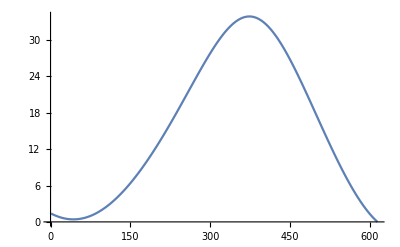

```mathematica
Max@Abs@ΩList 
ListLinePlot[Abs[Max@ΩList - ΩList]]
```

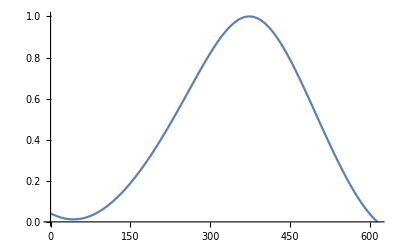

```mathematica
ΩListRe=Re[ΩList];
ΩListRe=Rescale@Abs[Max@ΩListRe - ΩListRe];
ListLinePlot[ΩListRe]
```

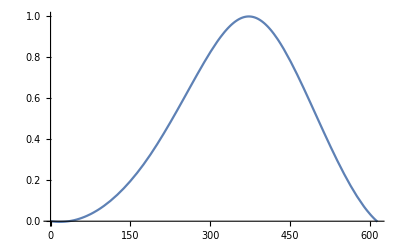

```mathematica
ΩFix=Transpose[{Range[0,nSteps-1],ΩListRe}];
nFix=200;
ΩFix=Prepend[ΩFix[[nFix;;]],{0,0}];
ΩFixFn=Interpolation[ΩFix,InterpolationOrder->2];
Plot[ΩFixFn[x],{x,0,nSteps}]
```

614

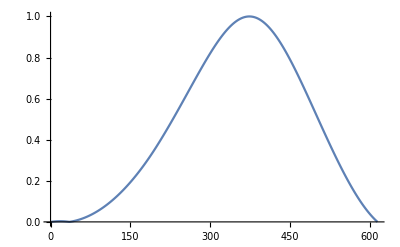

```mathematica
ΩListFix=Table[Abs@ΩFixFn[t],{t,0,nSteps-1}];
Length@ΩListFix
ListLinePlot[ΩListFix]
```

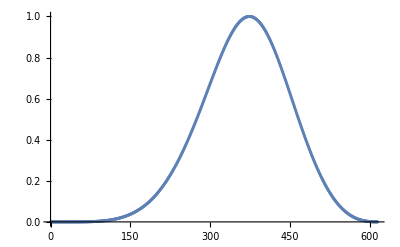

```mathematica
IntList=Rescale[ΩListFix^2];
ListPlot[IntList]
```

```mathematica
genSpecFolder=StringJoin[Riffle[ToString/@Round[Join[{g,κ,γ}/(2Pi),{η}],0.1],{"g_","kappa_","gamma_","eff"}]];
folderName="C:\\Users\\apc\\Documents\\Python Scripts\\Cold Control Heavy\\waveforms\\new_Tom\\Sin2 wavepacket\\"<>genSpecFolder<>"\\"<>ToString@nSteps<>" long";
If[DirectoryQ[folderName],None,CreateDirectory[folderName]]
δ=10^-5;
Table[
Export[folderName<>"\\sin2_"<>ToString[i]<>"_"<>ToString@nSteps<>".csv",N@Chop[{i/100 IntList},δ]],
{i,5,100,5}
]
```

C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 wavepacket\4.7g_1.8kappa_3.gamma_0.5eff\614 long

{C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 wavepacket\4.7g_1.8kappa_3.gamma_0.5eff\614 long\sin2_5_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 wavepacket\4.7g_1.8kappa_3.gamma_0.5eff\614 long\sin2_10_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 wavepacket\4.7g_1.8kappa_3.gamma_0.5eff\614 long\sin2_15_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 wavepacket\4.7g_1.8kappa_3.gamma_0.5eff\614 long\sin2_20_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 wavepacket\4.7g_1.8kappa_3.gamma_0.5eff\614 long\sin2_25_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 wavepacket\4.7g_1.8kappa_3.gamma_0.5eff\614 long\sin2_30_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 wavepacket\4.7g_1.8kappa_3.gamma_0.5eff\614 long\sin2_35_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 wavepacket\4.7g_1.8kappa_3.gamma_0.5eff\614 long\sin2_40_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 wavepacket\4.7g_1.8kappa_3.gamma_0.5eff\614 long\sin2_45_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 wavepacket\4.7g_1.8kappa_3.gamma_0.5eff\614 long\sin2_50_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 wavepacket\4.7g_1.8kappa_3.gamma_0.5eff\614 long\sin2_55_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 wavepacket\4.7g_1.8kappa_3.gamma_0.5eff\614 long\sin2_60_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 wavepacket\4.7g_1.8kappa_3.gamma_0.5eff\614 long\sin2_65_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 wavepacket\4.7g_1.8kappa_3.gamma_0.5eff\614 long\sin2_70_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 wavepacket\4.7g_1.8kappa_3.gamma_0.5eff\614 long\sin2_75_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 wavepacket\4.7g_1.8kappa_3.gamma_0.5eff\614 long\sin2_80_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 wavepacket\4.7g_1.8kappa_3.gamma_0.5eff\614 long\sin2_85_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 wavepacket\4.7g_1.8kappa_3.gamma_0.5eff\614 long\sin2_90_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 wavepacket\4.7g_1.8kappa_3.gamma_0.5eff\614 long\sin2_95_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 wavepacket\4.7g_1.8kappa_3.gamma_0.5eff\614 long\sin2_100_614.csv}

4.7g_1.8kappa_3.gamma_0.6eff

### Genenerate double hump

```mathematica
{g,κ,γ}={4.7,3.5/2,3}*2Pi;
η=0.40;

Coop=g^2/(2 κ γ);
ηgen = (2. Coop)/(2 Coop + 1)
```

0.807974

```mathematica
len=0.5;
nSteps=614;
tList=Range[0,len,len/(nSteps-1)];
Ω=ΩfuncDouble[len,η, g,κ,γ];
```

```mathematica
ΩList=Table[Ω[t],{t,tList}];
```

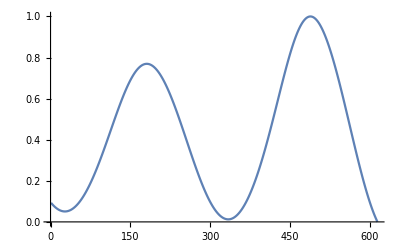

```mathematica
ΩListRe=Re[ΩList];
ListLinePlot[Rescale@Abs[Max@ΩListRe - ΩListRe]]
```

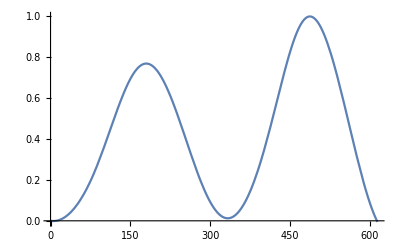

```mathematica
ΩFix=Transpose[{Range[0,nSteps-1],Rescale@Abs[Max@ΩListRe - ΩListRe]}];
nFix=80;
ΩFix=Prepend[ΩFix[[nFix;;]],{0,0}];
ΩFixFn=Interpolation[ΩFix,InterpolationOrder->2];
Plot[ΩFixFn[x],{x,0,nSteps}]
```

614

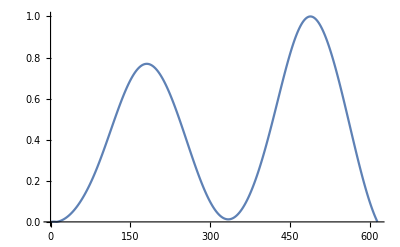

```mathematica
ΩListFix=Table[Abs@ΩFixFn[t],{t,0,nSteps-1}];
Length@ΩListFix
ListLinePlot[ΩListFix]
```

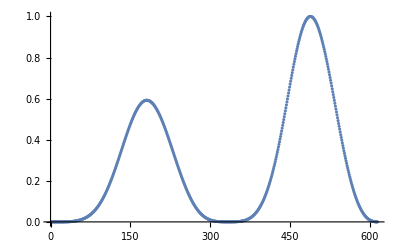

```mathematica
IntList=Rescale[ΩListFix^2];
ListPlot[IntList]
```

```mathematica
genSpecFolder=StringJoin[Riffle[ToString/@Round[Join[{g,κ,γ}/(2Pi),{η}],0.1],{"g_","kappa_","gamma_","eff"}]];
folderName="C:\\Users\\apc\\Documents\\Python Scripts\\Cold Control Heavy\\waveforms\\new_Tom\\Sin2 double wavepacket\\"<>genSpecFolder<>"\\"<>ToString@nSteps<>" long";
If[DirectoryQ[folderName],None,CreateDirectory[folderName]]
δ=10^-5;
Table[
Export[folderName<>"\\sin4_double_"<>ToString[i]<>"_"<>ToString@nSteps<>".csv",N@Chop[{i/100 ΩListFix},δ]],
{i,5,100,5}
]
```

C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 double wavepacket\4.7g_1.8kappa_3.gamma_0.4eff\614 long

{C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 double wavepacket\4.7g_1.8kappa_3.gamma_0.4eff\614 long\sin4_double_5_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 double wavepacket\4.7g_1.8kappa_3.gamma_0.4eff\614 long\sin4_double_10_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 double wavepacket\4.7g_1.8kappa_3.gamma_0.4eff\614 long\sin4_double_15_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 double wavepacket\4.7g_1.8kappa_3.gamma_0.4eff\614 long\sin4_double_20_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 double wavepacket\4.7g_1.8kappa_3.gamma_0.4eff\614 long\sin4_double_25_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 double wavepacket\4.7g_1.8kappa_3.gamma_0.4eff\614 long\sin4_double_30_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 double wavepacket\4.7g_1.8kappa_3.gamma_0.4eff\614 long\sin4_double_35_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 double wavepacket\4.7g_1.8kappa_3.gamma_0.4eff\614 long\sin4_double_40_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 double wavepacket\4.7g_1.8kappa_3.gamma_0.4eff\614 long\sin4_double_45_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 double wavepacket\4.7g_1.8kappa_3.gamma_0.4eff\614 long\sin4_double_50_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 double wavepacket\4.7g_1.8kappa_3.gamma_0.4eff\614 long\sin4_double_55_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 double wavepacket\4.7g_1.8kappa_3.gamma_0.4eff\614 long\sin4_double_60_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 double wavepacket\4.7g_1.8kappa_3.gamma_0.4eff\614 long\sin4_double_65_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 double wavepacket\4.7g_1.8kappa_3.gamma_0.4eff\614 long\sin4_double_70_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 double wavepacket\4.7g_1.8kappa_3.gamma_0.4eff\614 long\sin4_double_75_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 double wavepacket\4.7g_1.8kappa_3.gamma_0.4eff\614 long\sin4_double_80_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 double wavepacket\4.7g_1.8kappa_3.gamma_0.4eff\614 long\sin4_double_85_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 double wavepacket\4.7g_1.8kappa_3.gamma_0.4eff\614 long\sin4_double_90_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 double wavepacket\4.7g_1.8kappa_3.gamma_0.4eff\614 long\sin4_double_95_614.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin2 double wavepacket\4.7g_1.8kappa_3.gamma_0.4eff\614 long\sin4_double_100_614.csv}

4.7g_1.8kappa_3.gamma_0.6eff